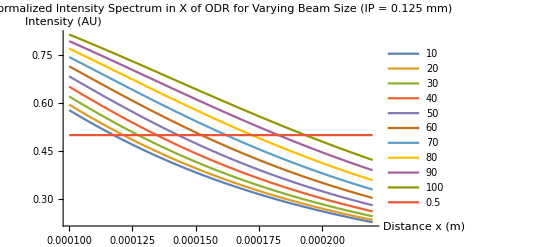

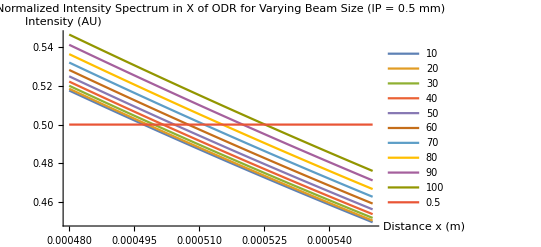

```mathematica
gamma=40000;
eps1=1;
eps2=11.9;
eps3=250;
c=299792458;
hbar=1.05457173*^-34;
beta=Sqrt[1-1/gamma^2];
e=1.602*^-19;
n=2*^10;(*number of electrons*)
q=n*e;(*bunch charge in Coulombs*)
rad=0.02 ;(*lense diameter in m*)
d=0.05 ;(*distance from foil to lens in m*)
a=0.00028280000000; (*size of diffraction slit in m*)
lowerlambda=300*^-9;(*Visible Spectrum m*)
averagelambda=500*^-9;
upperlambda=700*^-9;
eps0=8.854*^-12;
sigx=20*^-6;
sigy=sigx;
sigz=20*^-6;
alpha=7.297*^-3;
theta0=Pi/4;

thetalens=ArcTan[a/(2*d)];
thetamax=1/gamma;

Intensity1[ux_,uy_,sigx_,sigy_]:=
2*Pi*c*1/Pi^2*e^2/c*1/beta^2*n*1/(2*Pi*sigx*sigy)*NIntegrate[1/(gamma^2*lambda^2)*BesselK[1,1/(gamma*lambda)*Sqrt[(ux-x)^2+(uy-y)^2]]^2*Exp[-1/2*(x^2/sigx^2+y^2/sigy^2)],{x,-6*sigx,6*sigx},{y,-6*sigy,6*sigy},{lambda,lowerlambda,upperlambda},PrecisionGoal->6]

Intensity2[ux_,uy_,lambda_,sigx_,sigy_]:=
2*Pi*c*1/Pi^2*e^2/c*1/beta^2*n*1/(2*Pi*sigx*sigy)*NIntegrate[1/(gamma^2*lambda^4)*BesselK[1,1/(gamma*lambda)*Sqrt[(ux-x)^2+(uy-y)^2]]^2*Exp[-1/2*(x^2/sigx^2+y^2/sigy^2)],{x,-6*sigx,6*sigx},{y,-6*sigy,6*sigy},PrecisionGoal->6]

Intensity1[ux_,uy_,sigx_,sigy_]:=
2*Pi*c*1/Pi^2*e^2/c*1/beta^2*n*1/(2*Pi*sigx*sigy)*NIntegrate[1/(gamma^2*lambda^2)*BesselK[1,1/(gamma*lambda)*Sqrt[(ux-x)^2+(uy-y)^2]]^2*Exp[-1/2*(x^2/sigx^2+y^2/sigy^2)],{x,-6*sigx,6*sigx},{y,-6*sigy,6*sigy},{lambda,lowerlambda,upperlambda},PrecisionGoal->6]

Intensity2[ux_,uy_,lambda_,sigx_,sigy_]:=
2*Pi*c*1/Pi^2*e^2/c*1/beta^2*n*1/(2*Pi*sigx*sigy)*NIntegrate[1/(gamma^2*lambda^4)*BesselK[1,1/(gamma*lambda)*Sqrt[(ux-x)^2+(uy-y)^2]]^2*Exp[-1/2*(x^2/sigx^2+y^2/sigy^2)],{x,-6*sigx,6*sigx},{y,-6*sigy,6*sigy},PrecisionGoal->6]

Plot[{Intensity2[ux,125*^-6,averagelambda,10*^-6,sigy]/Intensity2[0,125*^-6,averagelambda,10*^-6,sigy],Intensity2[ux,125*^-6,averagelambda,20*^-6,sigy]/Intensity2[0,125*^-6,averagelambda,20*^-6,sigy],Intensity2[ux,125*^-6,averagelambda,30*^-6,sigy]/Intensity2[0,125*^-6,averagelambda,30*^-6,sigy],Intensity2[ux,125*^-6,averagelambda,40*^-6,sigy]/Intensity2[0,125*^-6,averagelambda,40*^-6,sigy],Intensity2[ux,125*^-6,averagelambda,50*^-6,sigy]/Intensity2[0,125*^-6,averagelambda,50*^-6,sigy],Intensity2[ux,125*^-6,averagelambda,60*^-6,sigy]/Intensity2[0,125*^-6,averagelambda,60*^-6,sigy],Intensity2[ux,125*^-6,averagelambda,70*^-6,sigy]/Intensity2[0,125*^-6,averagelambda,70*^-6,sigy],Intensity2[ux,125*^-6,averagelambda,80*^-6,sigy]/Intensity2[0,125*^-6,averagelambda,80*^-6,sigy],Intensity2[ux,125*^-6,averagelambda,90*^-6,sigy]/Intensity2[0,125*^-6,averagelambda,90*^-6,sigy],Intensity2[ux,125*^-6,averagelambda,100*^-6,sigy]/Intensity2[0,125*^-6,averagelambda,100*^-6,sigy],0.5},{ux,100*^-6,220*^-6},AxesLabel-> {"Distance x (m)","Intensity (AU)"},PlotLabel->"Normalized Intensity Spectrum in X of ODR for Varying Beam Size (IP = 0.125 mm)",PlotLegends->{"10","20","30","40","50","60","70","80","90","100","0.5"}]

Plot[{Intensity2[ux,500*^-6,averagelambda,10*^-6,sigy]/Intensity2[0,500*^-6,averagelambda,10*^-6,sigy],Intensity2[ux,500*^-6,averagelambda,20*^-6,sigy]/Intensity2[0,500*^-6,averagelambda,20*^-6,sigy],Intensity2[ux,500*^-6,averagelambda,30*^-6,sigy]/Intensity2[0,500*^-6,averagelambda,30*^-6,sigy],Intensity2[ux,500*^-6,averagelambda,40*^-6,sigy]/Intensity2[0,500*^-6,averagelambda,40*^-6,sigy],Intensity2[ux,500*^-6,averagelambda,50*^-6,sigy]/Intensity2[0,500*^-6,averagelambda,50*^-6,sigy],Intensity2[ux,500*^-6,averagelambda,60*^-6,sigy]/Intensity2[0,500*^-6,averagelambda,60*^-6,sigy],Intensity2[ux,500*^-6,averagelambda,70*^-6,sigy]/Intensity2[0,500*^-6,averagelambda,70*^-6,sigy],Intensity2[ux,500*^-6,averagelambda,80*^-6,sigy]/Intensity2[0,500*^-6,averagelambda,80*^-6,sigy],Intensity2[ux,500*^-6,averagelambda,90*^-6,sigy]/Intensity2[0,500*^-6,averagelambda,90*^-6,sigy],Intensity2[ux,500*^-6,averagelambda,100*^-6,sigy]/Intensity2[0,500*^-6,averagelambda,100*^-6,sigy],0.5},{ux,480*^-6,550*^-6},AxesLabel-> {"Distance x (m)","Intensity (AU)"},PlotLabel->"Normalized Intensity Spectrum in X of ODR for Varying Beam Size (IP = 0.5 mm)",PlotLegends->{"10","20","30","40","50","60","70","80","90","100","0.5"}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

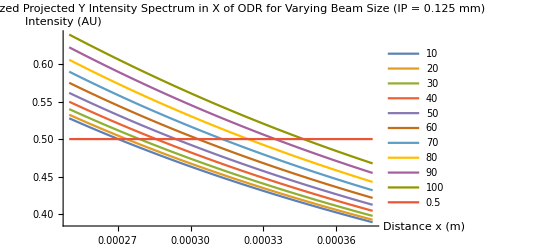

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

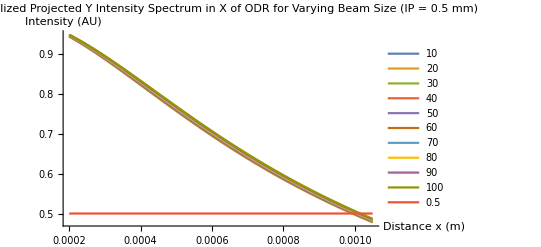

```mathematica
gamma=40000;
eps1=1;
eps2=11.9;
eps3=250;
c=299792458;
hbar=1.05457173*^-34;
beta=Sqrt[1-1/gamma^2];
e=1.602*^-19;
n=2*^10;(*number of electrons*)
q=n*e;(*bunch charge in Coulombs*)
rad=0.02 ;(*lense diameter in m*)
d=0.05 ;(*distance from foil to lens in m*)
a=0.00028280000000; (*size of diffraction slit in m*)
lowerlambda=300*^-9;(*Visible Spectrum m*)
averagelambda=500*^-9;
upperlambda=700*^-9;
eps0=8.854*^-12;
sigx=20*^-6;
sigy=sigx;
sigz=20*^-6;
alpha=7.297*^-3;
theta0=Pi/4;

thetalens=ArcTan[a/(2*d)];
thetamax=1/gamma;

IntensityX[ux_,a_,uymax_,lambda_,sigx_,sigy_]:=
2*Pi*c*1/Pi^2*e^2/c*1/beta^2*n*1/(2*Pi*sigx*sigy)*NIntegrate[1/(gamma^2*lambda^4)*BesselK[1,1/(gamma*lambda)*Sqrt[(ux-x)^2+(uy-y)^2]]^2*Exp[-1/2*(x^2/sigx^2+y^2/sigy^2)],{x,-6*sigx,6*sigx},{y,-6*sigy,6*sigy},{uy,a,uymax},PrecisionGoal->6]
IntensityY[uxwidth_,uy_,lambda_,sigx_,sigy_] :=
2*Pi*c*1/Pi^2*e^2/c*1/beta^2*n*1/(2*Pi*sigx*sigy)*NIntegrate[1/(gamma^2*lambda^4)*BesselK[1,1/(gamma*lambda)*Sqrt[(ux-x)^2+(uy-y)^2]]^2*Exp[-1/2*(x^2/sigx^2+y^2/sigy^2)],{x,-6*sigx,6*sigx},{y,-6*sigy,6*sigy},{ux,-uxwidth,uxwidth},PrecisionGoal->6]

Plot[{IntensityX[ux,125*^-6,0.005,averagelambda,10*^-6,sigy]/IntensityX[0,125*^-6,0.005,averagelambda,10*^-6,sigy],IntensityX[ux,125*^-6,0.005,averagelambda,20*^-6,sigy]/IntensityX[0,125*^-6,0.005,averagelambda,20*^-6,sigy],IntensityX[ux,125*^-6,0.005,averagelambda,30*^-6,sigy]/IntensityX[0,125*^-6,0.005,averagelambda,30*^-6,sigy],IntensityX[ux,125*^-6,0.005,averagelambda,40*^-6,sigy]/IntensityX[0,125*^-6,0.005,averagelambda,40*^-6,sigy],IntensityX[ux,125*^-6,0.005,averagelambda,50*^-6,sigy]/IntensityX[0,125*^-6,0.005,averagelambda,50*^-6,sigy],IntensityX[ux,125*^-6,0.005,averagelambda,60*^-6,sigy]/IntensityX[0,125*^-6,0.005,averagelambda,60*^-6,sigy],IntensityX[ux,125*^-6,0.005,averagelambda,70*^-6,sigy]/IntensityX[0,125*^-6,0.005,averagelambda,70*^-6,sigy],IntensityX[ux,125*^-6,0.005,averagelambda,80*^-6,sigy]/IntensityX[0,125*^-6,0.005,averagelambda,80*^-6,sigy],IntensityX[ux,125*^-6,0.005,averagelambda,90*^-6,sigy]/IntensityX[0,125*^-6,0.005,averagelambda,90*^-6,sigy],IntensityX[ux,125*^-6,0.005,averagelambda,100*^-6,sigy]/IntensityX[0,125*^-6,0.005,averagelambda,100*^-6,sigy],0.5},{ux,250*^-6,375*^-6},AxesLabel-> {"Distance x (m)","Intensity (AU)"},PlotLabel->"Normalized Projected Y Intensity Spectrum in X of ODR for Varying Beam Size (IP = 0.125 mm)",PlotLegends->{"10","20","30","40","50","60","70","80","90","100","0.5"}]

Plot[{IntensityX[ux,500*^-6,0.005,averagelambda,10*^-6,sigy]/IntensityX[0,500*^-6,averagelambda,10*^-6,sigy],IntensityX[ux,500*^-6,0.005,averagelambda,20*^-6,sigy]/IntensityX[0,500*^-6,0.005,averagelambda,20*^-6,sigy],IntensityX[ux,500*^-6,0.005,averagelambda,30*^-6,sigy]/IntensityX[0,500*^-6,0.005,averagelambda,30*^-6,sigy],IntensityX[ux,500*^-6,0.005,averagelambda,40*^-6,sigy]/IntensityX[0,500*^-6,0.005,averagelambda,40*^-6,sigy],IntensityX[ux,500*^-6,0.005,averagelambda,50*^-6,sigy]/IntensityX[0,500*^-6,0.005,averagelambda,50*^-6,sigy],IntensityX[ux,500*^-6,0.005,averagelambda,60*^-6,sigy]/IntensityX[0,500*^-6,0.005,averagelambda,60*^-6,sigy],IntensityX[ux,500*^-6,0.005,averagelambda,70*^-6,sigy]/IntensityX[0,500*^-6,0.005,averagelambda,70*^-6,sigy],IntensityX[ux,500*^-6,0.005,averagelambda,80*^-6,sigy]/IntensityX[0,500*^-6,0.005,averagelambda,80*^-6,sigy],IntensityX[ux,500*^-6,0.005,averagelambda,90*^-6,sigy]/IntensityX[0,500*^-6,0.005,averagelambda,90*^-6,sigy],IntensityX[ux,500*^-6,0.005,averagelambda,100*^-6,sigy]/IntensityX[0,500*^-6,0.005,averagelambda,100*^-6,sigy],0.5},{ux,200*^-6,1050*^-6},AxesLabel-> {"Distance x (m)","Intensity (AU)"},PlotLabel->"Normalized Projected Y Intensity Spectrum in X of ODR for Varying Beam Size (IP = 0.5 mm)",PlotLegends->{"10","20","30","40","50","60","70","80","90","100","0.5"}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

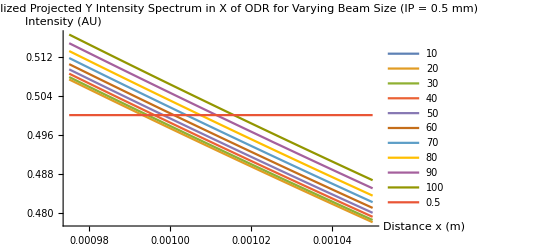

```mathematica
gamma=40000;
eps1=1;
eps2=11.9;
eps3=250;
c=299792458;
hbar=1.05457173*^-34;
beta=Sqrt[1-1/gamma^2];
e=1.602*^-19;
n=2*^10;(*number of electrons*)
q=n*e;(*bunch charge in Coulombs*)
rad=0.02 ;(*lense diameter in m*)
d=0.05 ;(*distance from foil to lens in m*)
a=0.00028280000000; (*size of diffraction slit in m*)
lowerlambda=300*^-9;(*Visible Spectrum m*)
averagelambda=500*^-9;
upperlambda=700*^-9;
eps0=8.854*^-12;
sigx=20*^-6;
sigy=sigx;
sigz=20*^-6;
alpha=7.297*^-3;
theta0=Pi/4;

thetalens=ArcTan[a/(2*d)];
thetamax=1/gamma;

IntensityX[ux_,a_,uymax_,lambda_,sigx_,sigy_]:=
2*Pi*c*1/Pi^2*e^2/c*1/beta^2*n*1/(2*Pi*sigx*sigy)*NIntegrate[1/(gamma^2*lambda^4)*BesselK[1,1/(gamma*lambda)*Sqrt[(ux-x)^2+(uy-y)^2]]^2*Exp[-1/2*(x^2/sigx^2+y^2/sigy^2)],{x,-6*sigx,6*sigx},{y,-6*sigy,6*sigy},{uy,a,uymax},PrecisionGoal->6]
IntensityY[uxwidth_,uy_,lambda_,sigx_,sigy_] :=
2*Pi*c*1/Pi^2*e^2/c*1/beta^2*n*1/(2*Pi*sigx*sigy)*NIntegrate[1/(gamma^2*lambda^4)*BesselK[1,1/(gamma*lambda)*Sqrt[(ux-x)^2+(uy-y)^2]]^2*Exp[-1/2*(x^2/sigx^2+y^2/sigy^2)],{x,-6*sigx,6*sigx},{y,-6*sigy,6*sigy},{ux,-uxwidth,uxwidth},PrecisionGoal->6]

Plot[{IntensityX[ux,500*^-6,0.005,averagelambda,10*^-6,sigy]/IntensityX[0,500*^-6,averagelambda,10*^-6,sigy],IntensityX[ux,500*^-6,0.005,averagelambda,20*^-6,sigy]/IntensityX[0,500*^-6,0.005,averagelambda,20*^-6,sigy],IntensityX[ux,500*^-6,0.005,averagelambda,30*^-6,sigy]/IntensityX[0,500*^-6,0.005,averagelambda,30*^-6,sigy],IntensityX[ux,500*^-6,0.005,averagelambda,40*^-6,sigy]/IntensityX[0,500*^-6,0.005,averagelambda,40*^-6,sigy],IntensityX[ux,500*^-6,0.005,averagelambda,50*^-6,sigy]/IntensityX[0,500*^-6,0.005,averagelambda,50*^-6,sigy],IntensityX[ux,500*^-6,0.005,averagelambda,60*^-6,sigy]/IntensityX[0,500*^-6,0.005,averagelambda,60*^-6,sigy],IntensityX[ux,500*^-6,0.005,averagelambda,70*^-6,sigy]/IntensityX[0,500*^-6,0.005,averagelambda,70*^-6,sigy],IntensityX[ux,500*^-6,0.005,averagelambda,80*^-6,sigy]/IntensityX[0,500*^-6,0.005,averagelambda,80*^-6,sigy],IntensityX[ux,500*^-6,0.005,averagelambda,90*^-6,sigy]/IntensityX[0,500*^-6,0.005,averagelambda,90*^-6,sigy],IntensityX[ux,500*^-6,0.005,averagelambda,100*^-6,sigy]/IntensityX[0,500*^-6,0.005,averagelambda,100*^-6,sigy],0.5},{ux,975*^-6,1050*^-6},AxesLabel-> {"Distance x (m)","Intensity (AU)"},PlotLabel->"Normalized Projected Y Intensity Spectrum in X of ODR for Varying Beam Size (IP = 0.5 mm)",PlotLegends->{"10","20","30","40","50","60","70","80","90","100","0.5"}]
```